```mathematica
colorMatchData={{0.38,0.0683,-0.0819,1.0136,0.0055},{0.385,0.0683,-0.0819,1.0136,0.0055},{0.39,0.0683,-0.0819,1.0136,0.0055},{0.395,0.0683,-0.0819,1.0136,0.0055},{0.40,0.0683,-0.0819,1.0136,0.0055},{0.405,0.0670,-0.0808,1.0138,0.0074},{0.41,0.0655,-0.0795,1.0140,0.0097},{0.415,0.0638,-0.0780,1.0142,0.0123},{0.42,0.0613,-0.0754,1.0141,0.0172},{0.425,0.0590,-0.0725,1.0135,0.0231},{0.43,0.0554,-0.0688,1.0134,0.0300},{0.435,0.0502,-0.0646,1.0144,0.0370},{0.44,0.0443,-0.0596,1.0153,0.0456},{0.445,0.0365,-0.0528,1.0163,0.0574},{0.45,0.0262,-0.0448,1.0186,0.0703},{0.455,0.0130,-0.0327,1.0197,0.0919},{0.46,-0.0030,-0.0175,1.0205,0.1194},{0.465,-0.0255,0.0056,1.0199,0.1629},{0.47,-0.0554,0.0420,1.0134,0.2359},{0.475,-0.0980,0.1010,0.9970,0.3592},{0.48,-0.1531,0.1843,0.9688,0.5374},{0.485,-0.2290,0.3125,0.9165,0.8190},{0.49,-0.3178,0.4839,0.8339,1.2061},{0.495,-0.4120,0.6964,0.7156,1.6992},{0.50,-0.5010,0.9247,0.5763,2.2392},{0.505,-0.5550,1.1290,0.4260,2.7437},{0.51,-0.5660,1.2870,0.2790,3.1594},{0.515,-0.5250,1.3670,0.1580,3.4086},{0.52,-0.4440,1.3620,0.0820,3.4625},{0.525,-0.3430,1.3020,0.0410,3.3850},{0.53,-0.2390,1.2230,0.0160,3.2590},{0.535,-0.1417,1.1410,0.0007,3.1194},{0.54,-0.0500,1.0590,-0.0090,2.9751},{0.545,0.0404,0.9740,-0.0144,2.8217},{0.55,0.1279,0.8890,-0.0169,2.6658},{0.555,0.2143,0.8030,-0.0173,2.5064},{0.56,0.2977,0.7190,-0.0167,2.3498},{0.565,0.3796,0.6360,-0.0156,2.1946},{0.57,0.4600,0.5540,-0.0140,2.0410},{0.575,0.5380,0.4740,-0.0120,1.8907},{0.58,0.6120,0.3980,-0.0100,1.7478},{0.585,0.6815,0.3270,-0.0085,1.6146},{0.59,0.7427,0.2640,-0.0067,1.4961},{0.595,0.7980,0.2070,-0.0050,1.3888},{0.60,0.8465,0.1570,-0.0035,1.2946},{0.605,0.8876,0.1150,-0.0026,1.2158},{0.61,0.9238,0.0780,-0.0018,1.1464},{0.615,0.9523,0.0490,-0.0013,1.0921},{0.62,0.9748,0.0260,-0.0008,1.0490},{0.625,0.9925,0.0078,-0.0003,1.0147},{0.63,1.0068,-0.0068,0.0000,0.9874},{0.635,1.0188,-0.0188,0.0000,0.9651},{0.64,1.0290,-0.0290,0.0000,0.9461},{0.645,1.0370,-0.0370,0.0000,0.9313},{0.65,1.0430,-0.0430,0.0000,0.9201},{0.655,1.0480,-0.0480,0.0000,0.9108},{0.66,1.0509,-0.0509,0.0000,0.9054},{0.665,1.0532,-0.0532,0.0000,0.9012},{0.67,1.0550,-0.0550,0.0000,0.8978},{0.675,1.0565,-0.0565,0.0000,0.8950},{0.68,1.0580,-0.0580,0.0000,0.8922},{0.685,1.0590,-0.0590,0.0000,0.8904},{0.69,1.0599,-0.0599,0.0000,0.8887},{0.695,1.0603,-0.0603,0.0000,0.8880},{0.70,1.0604,-0.0604,0.0000,0.8878}};
```

```mathematica
colorMatchData={#1*1000,#2,#3,#4}&@@@colorMatchData;
```

```mathematica
coeffA={#1,#2}&@@@colorMatchData;coeffB={#1,#3}&@@@colorMatchData;coeffC={#1,#4}&@@@colorMatchData;
```

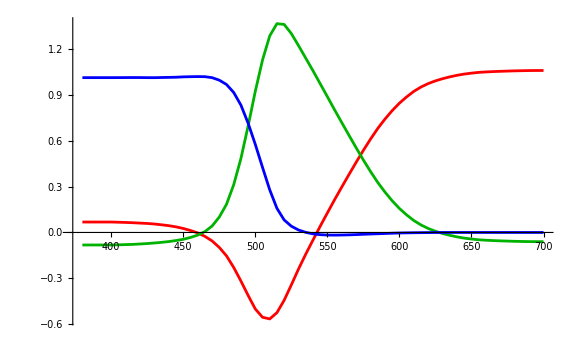
-Graphics-Normalized coefficients of each primary color to match the x-axis wavelengthwavelength of target color (nanometers)

```mathematica
Labeled[
ListLinePlot[{coeffA,coeffB,coeffC},PlotStyle->{Red,RGBColor[0,0.7,0],Blue}],
{"Normalized coefficients of each primary color to match the x-axis wavelength","wavelength of target color (nanometers)"},
{Top,Bottom}

]
```